```mathematica
ClearAll["Global`*"];
```

```mathematica
TA={{0.4,0.5},{0.6,1.375},{0.8,1.5},{1,1.75},{1.2,1.62}}
```

{{0.4,0.5},{0.6,1.375},{0.8,1.5},{1,1.75},{1.2,1.62}}

```mathematica
lgr[ta_,n_,x_]:=∑_(i=1)^n ta[[i,2]]*(∏_(j=1)^n If[j≠i,(x-ta[[j,1]])/(ta[[i,1]]-ta[[j,1]]),1]);
```

```mathematica
y[x_]:=lgr[TA,Length[TA],x]
y[z]
```

13.0208 (-1.2+z) (-1+z) (-0.8+z) (-0.6+z)-143.229 (-1.2+z) (-1+z) (-0.8+z) (-0.4+z)+234.375 (-1.2+z) (-1+z) (-0.6+z) (-0.4+z)-182.292 (-1.2+z) (-0.8+z) (-0.6+z) (-0.4+z)+42.1875 (-1+z) (-0.8+z) (-0.6+z) (-0.4+z)

```mathematica
y1[z_]:=Expand[y[z]]
```

```mathematica
y1[z]
```

-13.9+76.9833 z-144.25 z^2+118.854 z^3-35.9375 z^4

```mathematica
q1=lgr[TA,Length[TA],x];q2=InterpolatingPolynomial[TA,x];
yp[z_]:=InterpolatingPolynomial[TA,z]
```

```mathematica
yp[z]
Expand[yp[z]]
```

1.62+(1.4+(-2.75+(11.0417-35.9375 (-0.6+z)) (-0.8+z)) (-0.4+z)) (-1.2+z)

-13.9+76.9833 z-144.25 z^2+118.854 z^3-35.9375 z^4

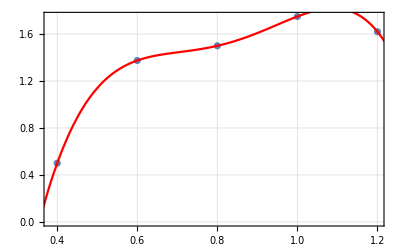

```mathematica
Show[ListPlot[TA],Plot[q1,{z,0,5},PlotStyle->Black],Plot[q2,{x,0,5},PlotStyle->Red],Frame->True, GridLines->Automatic]
```

```mathematica
f[x_]:=√x-2*Cos[x];
fn[x_,n_]:=Dt[f[x], {x,n}];
f5[x_]=N[fn[x,5]]; f5[x]
```

3.28125/x^(9/2)+2. Sin[x]

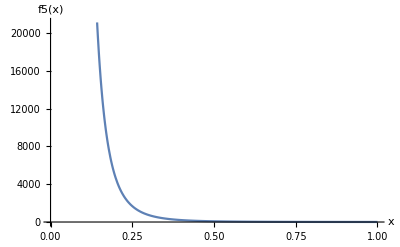

```mathematica
Plot[f5[x],{x,0,1},AxesLabel->{"x","f5(x)"}]
```

```mathematica
m=Abs[f5[0.25]]
```

1680.49

```mathematica
om[ta_,n_,x_]:=∏_(i=1)^n (x-ta[[i]]);
```

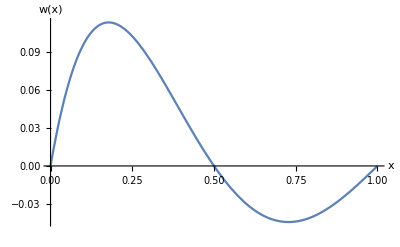

```mathematica
TA1={0,0.5,1,1.5,2,2.5};
Plot[om[TA1,Length[TA],x],{x,0,1}, AxesLabel->{"x", "w(x)"}]
```

```mathematica
mf=FindMinimum[om[TA1,Length[TA1],x],{x,1}]
```

{-0.0549316,{x→1.25}}

```mathematica
ri=m*Abs[mf[[1]]]/5!
```

0.769269

```mathematica
f1=Table[{TA1[[i]],f[TA1[[i]]]},{i,1,5}]
```

{{0,-2},{0.5,-1.04806},{1,1-2 Cos[1]},{1.5,1.08327},{2,√2-2 Cos[2]}}

```mathematica
ipol=Simplify[InterpolatingPolynomial[f1,x]]
```

-2.+2.19796 x-1.02374 x^2+0.99715 x^3-0.251979 x^4

```mathematica
r=Simplify[f[x]-ipol]
```

2.+√x-2.19796 x+1.02374 x^2-0.99715 x^3+0.251979 x^4-2 Cos[x]

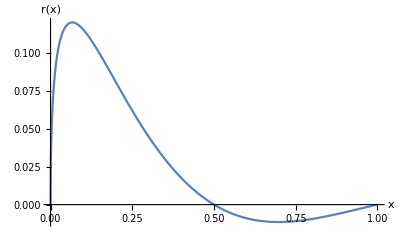

```mathematica
Plot[r,{x,0,1}, AxesLabel->{"x","r(x)"}]
```

```mathematica
rmax=FindMaximum[r,{x,1}]
```

{0.00715343,{x→1.25397}}

```mathematica
(*Рациональный выбор узлов*)
```

```mathematica
a=0;b= 2.5;n=Length[TA1]-1;
```

```mathematica
Do[y[i]=-Cos[(2*(i-1)+1)/(2*n+2)* π];Uzel[i]=N[(b+a)/2+(b-a)/2*y[i]],{i,1,n+1}];
TA2=Table[Uzel[i],{i,n+1}]
```

{0.0425927,0.366117,0.926476,1.57352,2.13388,2.45741}

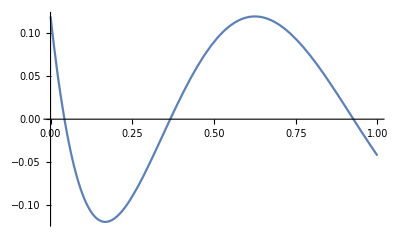

```mathematica
Plot[om[TA2,Length[TA2],x],{x,0,1}]
```

```mathematica
mf2=FindMinimum[om[TA2,Length[TA2],x],{x,1}]
```

{-0.119209,{x→1.25}}

```mathematica
ri2=m*Abs[mf2[[1]]]/5!
```

1.66942

```mathematica
f12=Table[{TA2[[i]],f[TA2[[i]]]},{i,1,5}]
```

{{0.0425927,-1.79181},{0.366117,-1.26237},{0.926476,-0.238774},{1.57352,1.25986},{2.13388,2.52838}}

```mathematica
ipol2=Simplify[InterpolatingPolynomial[f12,x]]
```

-1.86405+1.7122 x-0.401626 x^2+0.649961 x^3-0.180756 x^4

```mathematica
r2=Simplify[f[x]-ipol2]
```

1.86405+√x-1.7122 x+0.401626 x^2-0.649961 x^3+0.180756 x^4-2 Cos[x]

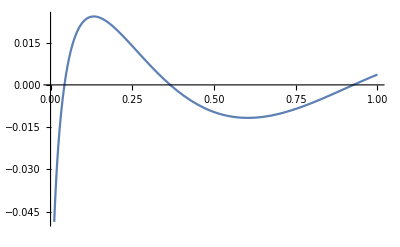

```mathematica
Plot[r2,{x,0,1}]
```

```mathematica
rmax2=FindMinimum[r2,{x,0.2}]
```

{-0.0117252,{x→0.603536}}